```mathematica
νp=({{1, 1, 3}, {0, 0, 0}});
νr=({{0, 0, 2}, {0, 1, 1}});
S=(νp-νr);S//MatrixForm
```

(1 | 1 | 1
0 | -1 | -1)

```mathematica
MM = MatrixRank[S];
CL = Transpose@NullSpace[Transpose@S];
CC = NullSpace[S];
{NN,RR} = Dimensions[S];
SubPlus[λ][ρ_] :=SubPlus[k][ρ]Product[x[i]^νr[[i,ρ]],{i,1,NN}];SubMinus[λ][ρ_]:=SubMinus[k][ρ]Product[x[i]^νp[[i,ρ]],{i,1,NN}];
rates = { SubPlus[k][1] -> 1,SubMinus[k][1]->1,SubPlus[k] [2] ->1 , SubMinus[k][2]-> α,SubPlus[k][3]-> β,  SubMinus[k][3]->1}
J =Table[SubPlus[λ][ρ]- SubMinus[λ][ρ],{ρ,1,RR}];
J /.rates//MatrixForm
```

{k_+[1]→1,k_-[1]→1,k_+[2]→1,k_-[2]→α,k_+[3]→β,k_-[3]→1}

(1-x[1]
-α x[1]+x[2]
-x[1]^3+β x[1]^2 x[2])

```mathematica
A = S.J;A /.rates//MatrixForm
```

(1-x[1]-α x[1]-x[1]^3+x[2]+β x[1]^2 x[2]
α x[1]+x[1]^3-x[2]-β x[1]^2 x[2])

```mathematica
SubStar[x] = Solve[A == 0, Table[x[i],{i,1,NN}]][[1]];SubStar[x]/.rates //FullSimplify
```

{x[1]→1,x[2]→(1+α)/(1+β)}

```mathematica
SubStar[J]= J /. SubStar[x]; SubStar[J]/.rates//FullSimplify
```

{0,(1-α β)/(1+β),(-1+α β)/(1+β)}

```mathematica
Subscript[A, (1)] = Together@FullSimplify@Grad[A,{x[1],x[2]}]/. SubStar[x];Subscript[A, (1)]/.rates
```

{{-4-α+(2 (1+α) β)/(1+β),1+β},{3+α-(2 (1+α) β)/(1+β),-1-β}}

```mathematica
DD = FullSimplify[Det[Subscript[A, (1)]]]/.rates
```

1+β

```mathematica
T =FullSimplify[ Tr[Subscript[A, (1)]]]/.rates //Together
```

(-5-α-4 β+α β-β^2)/(1+β)

```mathematica
Subscript[α, c]=Solve[T==0,α][[1]]//FullSimplify
```

{α→5+10/(-1+β)+β}

```mathematica
Eigenvalues[Subscript[A, (1)]]/.rates/. Subscript[α, c]//FullSimplify
```

{(1+β)^2/(√(-(1+β)^3)),(√(-(1+β)^3))/(1+β)}

```mathematica
Subscript[F, t] = A/. Table[x[i]->x[i][t],{i,1,NN}]/.rates
```

{1-x[1][t]-α x[1][t]-(x[1][t])^3+x[2][t]+β (x[1][t])^2 x[2][t],α x[1][t]+(x[1][t])^3-x[2][t]-β (x[1][t])^2 x[2][t]}

```mathematica
Subscript[α, c]/.{β ->3,ϵ->0.1}
```

{α→13}

```mathematica
par = {α ->31.001,β ->3,ϵ->0.1}
```

{α→31.001,β→3,ϵ→0.1}

```mathematica
SubStar[vecx]=Table[x[i],{i,1,NN}]/. SubStar[x]/.rates/.par
```

{1,8.00025}

```mathematica
EQS=Table[D[x[i][t],t]==Subscript[F, t][[i]],{i,1,NN}]/.par;EQS//MatrixForm
IC={x[1][0]==SubStar[vecx][[1]]+1,x[2][0]==SubStar[vecx][[2]]+1};
vars = Table[x[i][t],{i,1,NN}];
```

(x[1]'[t]==1-32.001 x[1][t]-(x[1][t])^3+x[2][t]+3 (x[1][t])^2 x[2][t]
x[2]'[t]==31.001 x[1][t]+(x[1][t])^3-x[2][t]-3 (x[1][t])^2 x[2][t])

```mathematica
Subscript[t, max]=1000;
sols=NDSolve[{EQS,IC},vars,{t,0,Subscript[t, max]}][[1]]
```

{x[1][t]→InterpolatingFunction[{{0., 1000.}}, <>][t],x[2][t]→InterpolatingFunction[{{0., 1000.}}, <>][t]}

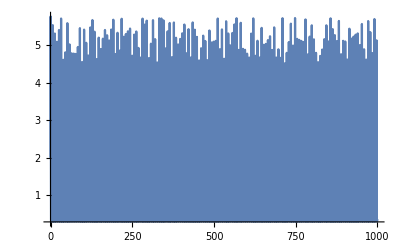

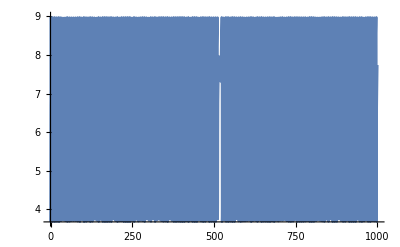

```mathematica
Plot[x[1][t]/.sols,{t,0,Subscript[t, max]},PlotRange->All]
Plot[x[2][t]/.sols,{t,0,Subscript[t, max]},PlotRange->All]
```

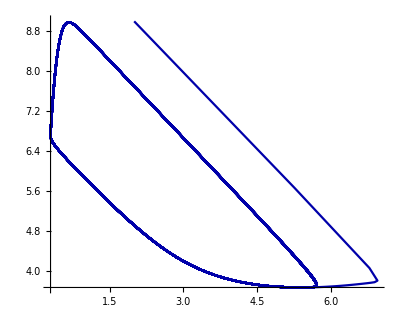

```mathematica
ParametricPlot[{x[1][t],x[2][t]}/.sols,{t,0,Subscript[t, max]},PlotRange->All,PlotPoints->1000,PlotStyle->Darker@Blue]
```

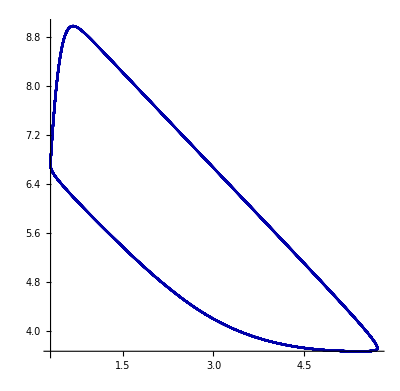

```mathematica
ParametricPlot[{x[1][t],x[2][t]}/.sols,{t,Subscript[t, max]*0.9,Subscript[t, max]},PlotRange->All,PlotPoints->200,PlotStyle->Darker@Blue]
```